# Generation of Data for Testing the Revised Calibration Software

## calibration algorithm/code: • Tsai-Wilson, • Kim, • DLT

## 0. Definition of the Parameters Used Throughout This Document

```mathematica
Needs["VectorAnalysis`"]
```

### 0.1 Raw parameters

The dimensions of all objects are given in millimeters but, in the end, image positions are given in pixels.  We follow Tsai & Wilson' s convention and define
	• Ncx, the number of sensor elements in the camera' s X direction (sels),
	• Nfx, the number of pixels in the frame grabber' s X direction (pixels),
	• dx, X dimension of a camera sensor element (mm/sel),
	• dy, Y dimension of a camera sensor element (mm/sel),
	• dpx effective X dimension of pixel in frame grabber (mm/pixel),
	• dpy effective Y dimension of pixel in frame grabber (mm/pixel).
  	• Cx, Cy, pixel coordinates of the true image center
	• sx, pixel h/v scaling ratio
To these parameters, we add the skewing parameter σ (see later)

```mathematica
myψ=N[π/6];
myθ=N[-π/8];
myφ = N[-π/6];
Subscript[myT, x]=-300.; (* mm *)
Subscript[myT, y]=100.; (* mm *)
Subscript[myT, z]=-2000; (* mm *)

myNcx=768;
myNcy=494;
mydx=0.005729166667; (* mm/sensor elt *)
mydy=0.006680161943; (* mm/sensor elt *)

myNfx=640;
myNfy=480;
myCx=320;
myCy=240;
mysx=1.0;

mydpx=mydx*myNcx/myNfx; (* mm/pixel *)
mydpy=mydy*myNcy/myNfy; 

myFoc=8.0; (* mm *)
Subscript[myκ, 1]=0.02;
myfpx=myFoc/mydpx; (* focal length in pixels *)
myfpy=myFoc/mydpy;
myσ=0.;
myskw=myσ*myfpy;

Subscript[myLargeκ, 1]=0.05;
myLargeσ=0.06;
myLargeSkw=myLargeσ*myfpy;
```

### 0.2 Definition of the substitution rule

```mathematica
projRules={ψ->myψ,θ->myθ,φ->myφ,Subscript[T, x]->Subscript[myT, x],Subscript[T, y]->Subscript[myT, y],Subscript[T, z]->Subscript[myT, z],Ncx->myNcx,Ncy->myNcy,dx->mydx,dy->mydy,Nfx->myNfx,Nfy->myNfy,Cx->myCx,Cy->myCy,sx->mysx,dpx->(mydx*myNcx/myNfx),dpy->mydpy,f->myFoc,Subscript[κ, 1]->Subscript[myκ, 1],σ->myσ,fpx->myfpx,fpy->myfpy,skw->myskw}
```

{ψ→0.523599,θ→-0.392699,φ→-0.523599,T_x→-300.,T_y→100.,T_z→-2000,Ncx→768,Ncy→494,dx→0.00572917,dy→0.00668016,Nfx→640,Nfy→480,Cx→320,Cy→240,sx→1.,dpx→0.006875,dpy→0.006875,f→8.,κ_1→0.02,σ→0.,fpx→1163.64,fpy→1163.64,skw→0.}

```mathematica
distortRules={Ncx->myNcx,Ncy->myNcy,dx->mydx,dy->mydy,Nfx->myNfx,Nfy->myNfy,Cx->myCx,Cy->myCy,sx->mysx,dpx->(mydx*myNcx/myNfx),dpy->mydpy,f->myFoc,Subscript[κ, 1]->Subscript[myLargeκ, 1],σ->myLargeσ,fpx->myfpx,fpy->myfpy,skw->myLargeSkw}
```

{Ncx→768,Ncy→494,dx→0.00572917,dy→0.00668016,Nfx→640,Nfy→480,Cx→320,Cy→240,sx→1.,dpx→0.006875,dpy→0.006875,f→8.,κ_1→0.05,σ→0.06,fpx→1163.64,fpy→1163.64,skw→69.8182}

## 1. Camera-toWorld Transformation: Extrinsic Parameters

### 1.1 Pose transform

#### 1.1.1 Translation term

The "world" and "camera" coordinate systems are different. We take for granted that the transformation between the two is expressend in the camera's coordinate system. It is given by :
	• a translation T={T_x, T_y, T_z},
	• a rotation specified by the yaw, pitch, and roll angles, ψ, θ, and φ respectively.

```mathematica
TransVec={Subscript[T, x],Subscript[T, y],Subscript[T, z]};
TransMat={{1,0,0,Subscript[T, x]},{0,1,0,Subscript[T, y]},{0,0,1,Subscript[T, z]},{0,0,0,1}};
MatrixForm[TransMat]
```

(1 | 0 | 0 | T_x
0 | 1 | 0 | T_y
0 | 0 | 1 | T_z
0 | 0 | 0 | 1)

#### 1.1.2 Construction of the rotation matrix

We assume that we apply Yaw, then Pitch, then Roll (around the fixed axes).

```mathematica
RotX={{1,0,0},{0,Cos[ψ],-Sin[ψ]},{0,Sin[ψ],Cos[ψ]}};
bigRotX={{1,0,0,0},{0,Cos[ψ],-Sin[ψ],0},{0,Sin[ψ],Cos[ψ],0},{0,0,0,1}};
```

```mathematica
MatrixForm[RotX]
MatrixForm[bigRotX]
```

(1 | 0 | 0
0 | Cos[ψ] | -Sin[ψ]
0 | Sin[ψ] | Cos[ψ])

(1 | 0 | 0 | 0
0 | Cos[ψ] | -Sin[ψ] | 0
0 | Sin[ψ] | Cos[ψ] | 0
0 | 0 | 0 | 1)

```mathematica
RotY={{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}};bigRotY={{Cos[θ],0,Sin[θ],0},{0,1,0,0},{-Sin[θ],0,Cos[θ],0},{0,0,0,1}};
```

```mathematica
MatrixForm[RotY]
MatrixForm[bigRotY]
```

(Cos[θ] | 0 | Sin[θ]
0 | 1 | 0
-Sin[θ] | 0 | Cos[θ])

(Cos[θ] | 0 | Sin[θ] | 0
0 | 1 | 0 | 0
-Sin[θ] | 0 | Cos[θ] | 0
0 | 0 | 0 | 1)

```mathematica
RotZ={{Cos[φ],-Sin[φ],0},{Sin[φ],Cos[φ],0},{0,0,1}};
bigRotZ={{Cos[φ],-Sin[φ],0,0},{Sin[φ],Cos[φ],0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
MatrixForm[RotZ]
MatrixForm[bigRotZ]
```

(Cos[φ] | -Sin[φ] | 0
Sin[φ] | Cos[φ] | 0
0 | 0 | 1)

(Cos[φ] | -Sin[φ] | 0 | 0
Sin[φ] | Cos[φ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
RotMat=RotZ.RotY.RotX;
bigRotMat=bigRotZ.bigRotY.bigRotX;
bigTransfMat=TransMat.bigRotZ.bigRotY.bigRotX;
MatrixForm[RotMat]
MatrixForm[bigRotMat]
MatrixForm[bigTransfMat]
```

(Cos[θ] Cos[φ] | -Cos[ψ] Sin[φ]+Cos[φ] Sin[θ] Sin[ψ] | Cos[φ] Cos[ψ] Sin[θ]+Sin[φ] Sin[ψ]
Cos[θ] Sin[φ] | Cos[φ] Cos[ψ]+Sin[θ] Sin[φ] Sin[ψ] | Cos[ψ] Sin[θ] Sin[φ]-Cos[φ] Sin[ψ]
-Sin[θ] | Cos[θ] Sin[ψ] | Cos[θ] Cos[ψ])

(Cos[θ] Cos[φ] | -Cos[ψ] Sin[φ]+Cos[φ] Sin[θ] Sin[ψ] | Cos[φ] Cos[ψ] Sin[θ]+Sin[φ] Sin[ψ] | 0
Cos[θ] Sin[φ] | Cos[φ] Cos[ψ]+Sin[θ] Sin[φ] Sin[ψ] | Cos[ψ] Sin[θ] Sin[φ]-Cos[φ] Sin[ψ] | 0
-Sin[θ] | Cos[θ] Sin[ψ] | Cos[θ] Cos[ψ] | 0
0 | 0 | 0 | 1)

(Cos[θ] Cos[φ] | -Cos[ψ] Sin[φ]+Cos[φ] Sin[θ] Sin[ψ] | Cos[φ] Cos[ψ] Sin[θ]+Sin[φ] Sin[ψ] | T_x
Cos[θ] Sin[φ] | Cos[φ] Cos[ψ]+Sin[θ] Sin[φ] Sin[ψ] | Cos[ψ] Sin[θ] Sin[φ]-Cos[φ] Sin[ψ] | T_y
-Sin[θ] | Cos[θ] Sin[ψ] | Cos[θ] Cos[ψ] | T_z
0 | 0 | 0 | 1)

#### 1.1.3 The complete change of coordinates

```mathematica
w2c[{Xw_,Yw_,Zw_}]=RotMat.{Xw,Yw,Zw}+TransVec;
```

### 1.2 Checking that it is OK

#### 1.2.1 Generation of 3D points in "World" coordinates

We generate a set of points in the world coordinate system and check that they look all right in the camera's coordinate system.

```mathematica
ptsPerRow=10;
PtsWorld=Flatten[Table[{100.j,150.i,10.0},{i,0,ptsPerRow-1},{j,0,ptsPerRow-1}],1];
```

#### 1.2.2 Visualization of the points in "World" coordinates

```mathematica
ListPointPlot3D[PtsWorld,PlotRange->{{0,1000},{0,1500},{0,200}}]
```

-Graphics3D-

#### 1.2.3 Visualization of the points in "Camera" coordinates

```mathematica
PtsCam=N[Map[w2c,PtsWorld]//.projRules];
```

```mathematica
ListPointPlot3D[PtsCam]
```

-Graphics3D-

## 2. Modeling the Perfect Camera

### 2.1 Perspective projection: pinhole model

#### 2.1.1 The classical pinhole model

I use -f in the projection equation because Z is negative and I want to keep a positive value for the focal length.

```mathematica
Proj[{X_,Y_,Z_}]={-f X/Z,-f Y/Z};
```

#### 2.1.2 Checking that it looks right

We project points that form a square grid on a vertical plane looked at from a 45 degree angle

```mathematica
theOrigin={-1000., 1000., 3000.};

ptsPerRow=10;

Pts3D=Flatten[Table[{100.j/√2,-100.i,100.j/√2}+theOrigin,{i,0,ptsPerRow-1},{j,0,ptsPerRow-1}],1];
```

```mathematica
Pts2D=N[Map[Proj,Pts3D]/.projRules];
```

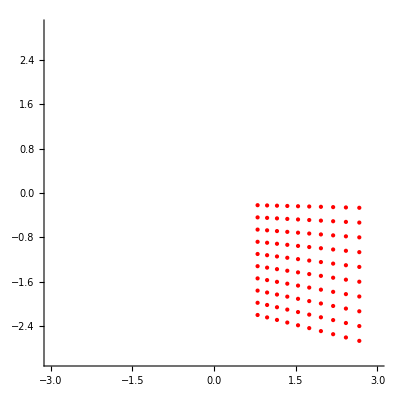

```mathematica
ListPlot[Pts2D,PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[1,0,0],AspectRatio->Automatic]
```

### 2.2 Millimeters to pixels

#### 2.2.1 Define intyyrinsic parameters

The dimensions of all objects are given in millimeters but, in the end, image positions are given in pixels.  We follow Tsai & Wilson's convention and define
	• Ncx, the number of sensor elements in the camera's X direction (sels),
	• Nfx, the number of pixels in the frame grabber's X direction (pixels),
	• dx, X dimension of a camera sensor element (mm/sel),
	• dy, Y dimension of a camera sensor element (mm/sel),
	• dpx effective X dimension of pixel in frame grabber (mm/pixel),
	• dpy effective Y dimension of pixel in frame grabber (mm/pixel).
	• Cx, Cy, pixel coordinates of the true image center
	• sx, pixel h/v scaling ratio

It is easy to check that dpx = (dx Ncx)/Nfx. One can assume that the same ratio (camera vs. frame grabber) is kept for the Y dimension, so that dpy = (dy Ncx)/Nfx

#### 2.2.2 First, the "integer pixels"

```mathematica
mm2pixel[{px_,py_}]={Round[px/dpx]+Cx,Round[py/dpy]+Cy};
```

#### 2.2.3 Then, the "float pixels"

```mathematica
mm2flPixel[{px_,py_}]={px/dpx+Cx,py/dpy+Cy};
```

### 2.3 Finally, check if the point is within image boundaries

```mathematica
isItIn[{x_,y_}]:=If[x<0 || x≥Nfx||y<0||y≥Nfy,0,1];
```

### 2.4 Inverse transformations

#### 2.4.1 Equations of the inverse transformation

```mathematica
pixel2mm[{x_,y_}]={Round[(x-Cx)*dpx],Round[(y-Cy)*dpy]};
```

```mathematica
flPixel2mm[{x_,y_}]={(x-Cx)*dpx,(y-Cy)*dpy};
```

#### 2.4.2 Verification

```mathematica
pixel2mm[mm2pixel[{100,200}]]//.distortRules
```

{100,200}

```mathematica
flPixel2mm[mm2flPixel[{100,200}]]//.distortRules
```

{100,200}

Obviously this one does not invert properly because of rounding error

```mathematica
mm2pixel[pixel2mm[{100,200}]]//.distortRules
```

{29,240}

```mathematica
mm2flPixel[flPixel2mm[{100,200}]]//.distortRules
```

{100,200}

## 3. Modeling the Imperfect Camera

### 3.1 Distortion and un-distortion

First we define the un-distortion transformation given by Tsai

```mathematica
UnDistort[md_]=(1+Subscript[κ, 1] md.md) md;
```

Next, we move on to distortion...
We have:  mu  = (1 + κ1 m2u) md , so if  we pose  md = α mu , we can solve for α ...

```mathematica
EquaCubique=Collect[α (1+Subscript[κ, 1] α^2 ru^2)-1,α]
```

-1+α+ru^2 α^3 κ_1

```mathematica
EquatoSolve=Collect[EquaCubique/(Subscript[κ, 1]  ru^2),α]
```

α^3-1/(ru^2 κ_1)+α/(ru^2 κ_1)

When the discriminant is  > 0 , only one solution is real. It happens to be the third in the output of the Solve function. When  the discriminant is  < 0 , there are three real solutions. Since  we always have p > 0, however, the latter case is not something we should waste time on.

```mathematica
αSol=Solve[α^3+p α-p==0,α]
```

{{α→-((2/3)^(1/3) p)/((9 p+√3 √(27 p^2+4 p^3))^(1/3))+((9 p+√3 √(27 p^2+4 p^3))^(1/3))/(2^(1/3) 3^(2/3))},{α→((1+ⅈ √3) p)/(2^(2/3) 3^(1/3) (9 p+√3 √(27 p^2+4 p^3))^(1/3))-((1-ⅈ √3) (9 p+√3 √(27 p^2+4 p^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{α→((1-ⅈ √3) p)/(2^(2/3) 3^(1/3) (9 p+√3 √(27 p^2+4 p^3))^(1/3))-((1+ⅈ √3) (9 p+√3 √(27 p^2+4 p^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}

We can now define the distorsion function:

```mathematica
Distort[mu_]=Block[{ru2=mu.mu,p=Evaluate[1/(Subscript[κ, 1] ru2)],BigTerm=(9 p+√3 √(27 p^2+4 p^3))^(1/3)},(-((2/3)^(1/3) p)/BigTerm+BigTerm/18^(1/3)) mu];
```

### 3.2 Checking that it works fine

#### 3.2.1 Distorsion and undistorsion invert each other

We check that the functions perform as expected.

```mathematica
N[Distort[UnDistort[{20.,30.}]]//.distortRules]
```

{20.,30.}

```mathematica
N[UnDistort[Distort[{50.,40.}]]//.distortRules]
```

{50.,40.}

#### 3.2.2 Distorsion looks good

Nb.: The units used for the distorsion equation are milimeters.

For our comparison of the method taking into account distortion vs. the one ignoring them, we will study the deformations of a rectangular set of points (in pixel units).

```mathematica
cRect={.2,.2};
side=2.;
half=side/2.0;
ptsPerRow=20;
ratio=side/ptsPerRow;
```

```mathematica
PixelSquare=Join[
Table[{i*ratio-half,-half}+cRect,{i,0,ptsPerRow}],Table[{half,i*ratio-half}+cRect,{i,0,ptsPerRow}],Table[{half-i*ratio,half}+cRect,{i,0,ptsPerRow}],Table[{-half,half-i*ratio}+cRect,{i,0,ptsPerRow}]];
```

```mathematica
DistortNum[mu_]=N[Distort[mu]/.distortRules];
```

```mathematica
notSoSquare=Map[DistortNum,PixelSquare];
```

Note that, for the time being, the "image" is displayed upside down , 'cause I dunno how  to  invert  the  orientation of the axes.

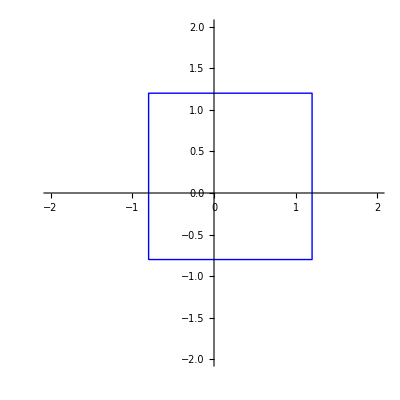

```mathematica
StraightRect=ListPlot[PixelSquare,PlotRange->{{-2,2},{-2,2}},Joined->True,PlotStyle->RGBColor[0,0,1],AspectRatio->Automatic]
```

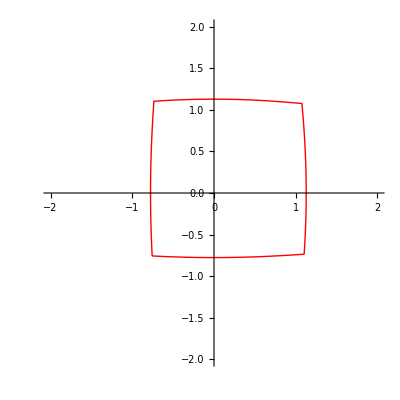

```mathematica
CrookyRect=ListPlot[notSoSquare,PlotRange->{{-2,2},{-2,2}},Joined->True,PlotStyle->RGBColor[1,0,0],AspectRatio->Automatic]
```

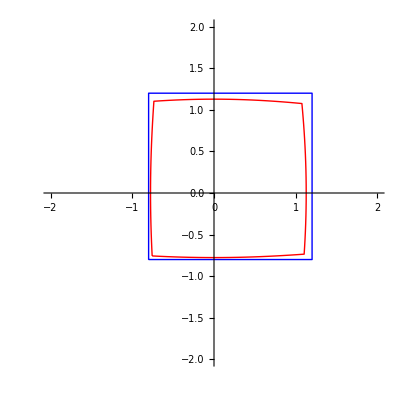

```mathematica
Show[StraightRect,CrookyRect]
```

### 3.3 Skewing and de-skewing

#### 3.3.1 Define the transformations

```mathematica
Skew[m_]:={{1,σ},{0,1}}.m;
```

```mathematica
Unskew[m_]:={{1,-σ},{0,1}}.m;
```

#### 3.3.2 Verify with the square

```mathematica
SkewedSquare=Map[Skew,PixelSquare]/.distortRules;
```

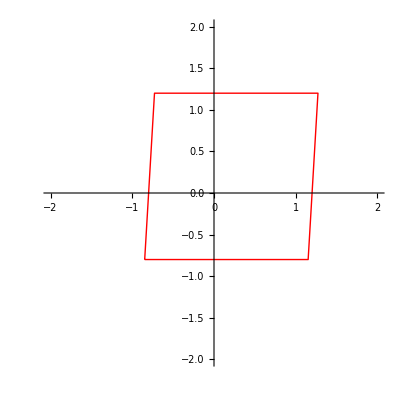

```mathematica
SkewedRect=ListPlot[SkewedSquare,PlotRange->{{-2,2},{-2,2}},Joined->True,PlotStyle->RGBColor[1,0,0],AspectRatio->Automatic]
```

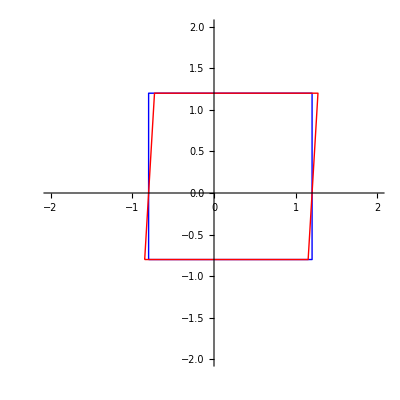

```mathematica
Show[StraightRect,SkewedRect]
```

```mathematica
StraightenedSquare=Map[Unskew,SkewedSquare]/.distortRules;
```

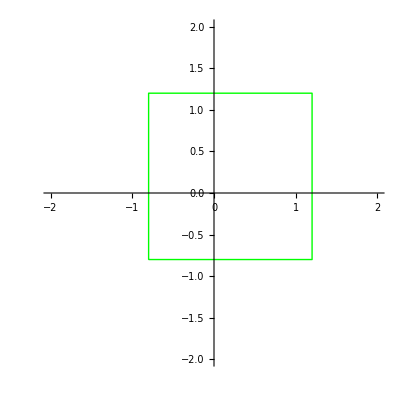

```mathematica
StraightenedRect=ListPlot[StraightenedSquare,PlotRange->{{-2,2},{-2,2}},Joined->True,PlotStyle->RGBColor[0,1,0],AspectRatio->Automatic]
```

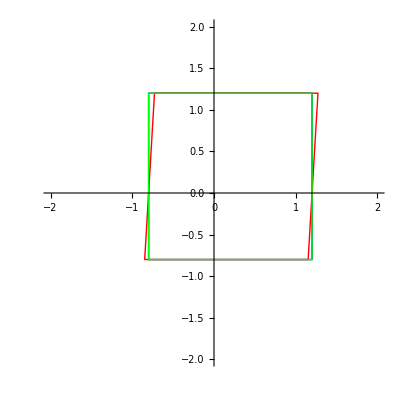

```mathematica
Show[StraightRect,SkewedRect,StraightenedRect]
```

### 3.4 The objects we will try to recompute

#### 3.4.1 The "state vector" of the Tsai calibration calculations

```mathematica
fullStateVec=Take[Flatten[bigTransfMat],12]//. projRules
```

{0.800103,0.267306,-0.537013,-300.,-0.46194,0.845671,-0.267306,100.,0.382683,0.46194,0.800103,-2000}

```mathematica
fullScaledStateVec=Take[Flatten[{{1,0,0,0},{0,1,0,0},{0,0,1/f,0},{0,0,0,1}}.bigTransfMat],12]//. projRules
```

{0.800103,0.267306,-0.537013,-300.,-0.46194,0.845671,-0.267306,100.,0.0478354,0.0577425,0.100013,-250.}

```mathematica
fullScaledNormalizedStateVec=fullScaledStateVec*(-1/fullScaledStateVec[[12]])
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052,-1.}

```mathematica
partialScaledStateVec=Take[fullScaledNormalizedStateVec,11]
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052}

Terms 1-3 and 5-7 of the partial scaled state vector are the first two rows of the rotation matrix scaled by (-f/Tz). The sum s of the squares of these terms should therefore be 2(f/Tz)^2. From this we can get Tz/f =-√(2/s). If we multiply the partial scaled state vector by this number, we should get back the full scaled vector. We can then use the nominal focal length to multiply terms 9-12 of the vector to get our computed full state vector.

```mathematica
ClearAll[v,partialScaleToFullStateVect]
```

```mathematica
partialScaleToFullStateVect[v_]:=Block[{s=√(2/(v[[1]]^2+v[[2]]^2+v[[3]]^2+v[[5]]^2+v[[6]]^2+v[[7]]^2)),newV=s*Append[v,-1]},{newV[[1]],newV[[2]],newV[[3]],newV[[4]],newV[[5]],newV[[6]],newV[[7]],newV[[8]],f*newV[[9]],f*newV[[10]],f*newV[[11]],f*newV[[12]]}//.projRules]
```

```mathematica
Chop[partialScaleToFullStateVect[partialScaledStateVec]-fullStateVec]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

#### 3.4.2 The projection matrix of the DLT algorithm

```mathematica
CalibMat={{-fpx,skw,Cx},{0,-fpy,Cy},{0,0,1}}/.projRules;
MatrixForm[CalibMat]
```

(-1163.64 | 0. | 320
0 | -1163.64 | 240
0 | 0 | 1)

```mathematica
ProjMat=CalibMat.{{1,0,0,0},{0,1,0,0},{0,0,1,0}}.bigTransfMat/.projRules;
MatrixForm[ProjMat]
```

(-808.57 | -163.226 | 880.92 | -290909.
629.374 | -873.188 | 503.072 | -596364.
0.382683 | 0.46194 | 0.800103 | -2000.)

```mathematica
ProjVect=Flatten[ProjMat]
```

{-808.57,-163.226,880.92,-290909.,629.374,-873.188,503.072,-596364.,0.382683,0.46194,0.800103,-2000.}

### 3.5 Decomposition of the projection matrix

#### 3.5.1 First, I work out the equation by starting with a generic 3x3 matrix M (upper-left 3-x3 subpart of P)

M = K R, with K upper triangular and R orthogonal, so the decomposition is unique.  We right-multiply M in sequence by 3 rotation matrices R_x, R_y, R_z that set to 0 respectively the terms (3,2), (3,1) and (2,1) of the matrix. In the end we get K=R_x R_y R_y and R =  R_z^TR_y^TR_z^T

```mathematica
M={{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}};
MatrixForm[M]
```

(m11 | m12 | m13
m21 | m22 | m23
m31 | m32 | m33)

```mathematica
{MRx,RxT}=Block[{c1=-m33/√(m32^2+m33^2),s1=m32/√(m32^2+m33^2),Rx={{1,0,0},{0,c1,-s1},{0,s1,c1}}},{M.Rx,Transpose[Rx]}];
MatrixForm[MRx]
MatrixForm[RxT]
```

(m11 | (m13 m32)/(√(m32^2+m33^2))-(m12 m33)/(√(m32^2+m33^2)) | -(m12 m32)/(√(m32^2+m33^2))-(m13 m33)/(√(m32^2+m33^2))
m21 | (m23 m32)/(√(m32^2+m33^2))-(m22 m33)/(√(m32^2+m33^2)) | -(m22 m32)/(√(m32^2+m33^2))-(m23 m33)/(√(m32^2+m33^2))
m31 | 0 | -m32^2/(√(m32^2+m33^2))-m33^2/(√(m32^2+m33^2)))

(1 | 0 | 0
0 | -m33/(√(m32^2+m33^2)) | m32/(√(m32^2+m33^2))
0 | -m32/(√(m32^2+m33^2)) | -m33/(√(m32^2+m33^2)))

```mathematica
M2={{m11,mp12,mp13},{m21,mp22,mp23},{m31,0,mp33}};
MatrixForm[M2]
```

(m11 | mp12 | mp13
m21 | mp22 | mp23
m31 | 0 | mp33)

```mathematica
{MRxRy,RyTRxT}=Block[{c2,s2},M2.{{c2,0,s2},{0,1,0},{-s2,0,c2}}];
MatrixForm[MRxRy]
```

Set::shape: Lists {MRxRy, RyTRxT} and {{c2\ m11 - mp13\ s2, mp12, c2\ mp13 + m11\ s2}, {c2\ m21 - mp23\ s2, mp22, c2\ mp23 + m21\ s2}, {c2\ m31 - mp33\ s2, 0, c2\ mp33 + m31\ s2}} are not the same shape.

MRxRy

```mathematica
{MRxRy,RyTRxT}=Block[{c2=mp33/√(m31^2+mp33^2),s2=m31/√(m31^2+mp33^2),Ry={{c2,0,s2},{0,1,0},{-s2,0,c2}}},{M2.Ry,Transpose[Ry].RxT}];
MatrixForm[MRxRy]
MatrixForm[RyTRxT]
```

(-(m31 mp13)/(√(m31^2+mp33^2))+(m11 mp33)/(√(m31^2+mp33^2)) | mp12 | (m11 m31)/(√(m31^2+mp33^2))+(mp13 mp33)/(√(m31^2+mp33^2))
-(m31 mp23)/(√(m31^2+mp33^2))+(m21 mp33)/(√(m31^2+mp33^2)) | mp22 | (m21 m31)/(√(m31^2+mp33^2))+(mp23 mp33)/(√(m31^2+mp33^2))
0 | 0 | m31^2/(√(m31^2+mp33^2))+mp33^2/(√(m31^2+mp33^2)))

(mp33/(√(m31^2+mp33^2)) | (m31 m32)/(√(m32^2+m33^2) √(m31^2+mp33^2)) | (m31 m33)/(√(m32^2+m33^2) √(m31^2+mp33^2))
0 | -m33/(√(m32^2+m33^2)) | m32/(√(m32^2+m33^2))
m31/(√(m31^2+mp33^2)) | -(m32 mp33)/(√(m32^2+m33^2) √(m31^2+mp33^2)) | -(m33 mp33)/(√(m32^2+m33^2) √(m31^2+mp33^2)))

```mathematica
M3={{mq11,mp12,mq13},{mq21,mp22,mq23},{0,0,mq33}};
MatrixForm[M3]
```

(mq11 | mp12 | mq13
mq21 | mp22 | mq23
0 | 0 | mq33)

```mathematica
MRxRyRz=Block[{c3,s3},M3.{{c3,-s3,0},{s3,c3,0},{0,0,1}}];
MatrixForm[MRxRyRz]
```

(c3 mq11+mp12 s3 | c3 mp12-mq11 s3 | mq13
c3 mq21+mp22 s3 | c3 mp22-mq21 s3 | mq23
0 | 0 | mq33)

```mathematica
{MRxRyRz,R}=Block[{c3=-mp22/√(mq21^2+mp22^2),s3=mq21/√(mq21^2+mp22^2),Rz={{c3,-s3,0},{s3,c3,0},{0,0,1}}},{M3.Rz,Transpose[Rz].RyTRxT}];
MatrixForm[MRxRyRz]
MatrixForm[R]
```

(-(mp22 mq11)/(√(mp22^2+mq21^2))+(mp12 mq21)/(√(mp22^2+mq21^2)) | -(mp12 mp22)/(√(mp22^2+mq21^2))-(mq11 mq21)/(√(mp22^2+mq21^2)) | mq13
0 | -mp22^2/(√(mp22^2+mq21^2))-mq21^2/(√(mp22^2+mq21^2)) | mq23
0 | 0 | mq33)

(-(mp22 mp33)/(√(m31^2+mp33^2) √(mp22^2+mq21^2)) | -(m31 m32 mp22)/(√(m32^2+m33^2) √(m31^2+mp33^2) √(mp22^2+mq21^2))-(m33 mq21)/(√(m32^2+m33^2) √(mp22^2+mq21^2)) | -(m31 m33 mp22)/(√(m32^2+m33^2) √(m31^2+mp33^2) √(mp22^2+mq21^2))+(m32 mq21)/(√(m32^2+m33^2) √(mp22^2+mq21^2))
-(mp33 mq21)/(√(m31^2+mp33^2) √(mp22^2+mq21^2)) | (m33 mp22)/(√(m32^2+m33^2) √(mp22^2+mq21^2))-(m31 m32 mq21)/(√(m32^2+m33^2) √(m31^2+mp33^2) √(mp22^2+mq21^2)) | -(m32 mp22)/(√(m32^2+m33^2) √(mp22^2+mq21^2))-(m31 m33 mq21)/(√(m32^2+m33^2) √(m31^2+mp33^2) √(mp22^2+mq21^2))
m31/(√(m31^2+mp33^2)) | -(m32 mp33)/(√(m32^2+m33^2) √(m31^2+mp33^2)) | -(m33 mp33)/(√(m32^2+m33^2) √(m31^2+mp33^2)))

#### 3.5.2 Now rewrite this as a procedure with the projection vector as input

```mathematica
DecomposeProjVect[PV_]:=Block[
{M={{PV[[1]],PV[[2]],PV[[3]]},{PV[[5]],PV[[6]],PV[[7]]},{PV[[9]],PV[[10]],PV[[11]]}},c1,s1,Rx,M2,RxT,c2,Ry,M3,RyTRxT,c3,s3,Rz},

c1=-M[[3]][[3]]/√((M[[3]][[2]])^2+(M[[3]][[3]])^2);
s1=M[[3]][[2]]/√((M[[3]][[2]])^2+(M[[3]][[3]])^2);
Rx={{1,0,0},{0,c1,-s1},{0,s1,c1}};
M2=M.Rx;
RxT=Transpose[Rx];

c2=M2[[3]][[3]]/√((M2[[3]][[1]])^2+(M2[[3]][[3]])^2);
s2=M2[[3]][[1]]/√((M2[[3]][[1]])^2+(M2[[3]][[3]])^2);
Ry={{c2,0,s2},{0,1,0},{-s2,0,c2}};
M3=M2.Ry;
RyTRxT=Transpose[Ry].RxT;

c3=-M3[[2]][[2]]/√((M3[[2]][[1]])^2+(M3[[2]][[2]])^2);
s3=M3[[2]][[1]]/√((M3[[2]][[1]])^2+(M3[[2]][[2]])^2);
Rz={{c3,-s3,0},{s3,c3,0},{0,0,1}};
{M3.Rz,Transpose[Rz].RyTRxT}];
```

```mathematica
{K,R}=Chop[N[DecomposeProjVect[ProjVect]]];
MatrixForm[K]
MatrixForm[R]
```

(-1163.64 | 0 | 320.
0 | -1163.64 | 240.
0 | 0 | 1.)

(0.800103 | 0.267306 | -0.537013
-0.46194 | 0.845671 | -0.267306
0.382683 | 0.46194 | 0.800103)

## 4. Generation of image data points

#### 4.1.3 Definition of plotting ranges

```mathematica
PixelPlotRange={{0,Nfx-1},{0,Nfy-1}}/.projRules
```

{{0,639},{0,479}}

```mathematica
MetricPlotRange=1.1*{{-Ncx*dx/2,Ncx*dx/2},{-Ncy*dy/2,Ncy*dy/2}}/.projRules
```

{{-2.42,2.42},{-1.815,1.815}}

#### 4.1.4 The rotation and translation matrices

```mathematica
MatrixForm[N[RotMat//.projRules]]
```

(0.800103 | 0.267306 | -0.537013
-0.46194 | 0.845671 | -0.267306
0.382683 | 0.46194 | 0.800103)

```mathematica
MatrixForm[N[bigTransfMat//.projRules]]
```

(0.800103 | 0.267306 | -0.537013 | -300.
-0.46194 | 0.845671 | -0.267306 | 100.
0.382683 | 0.46194 | 0.800103 | -2000.
0. | 0. | 0. | 1.)

#### 4.1.5 Just to make sure that I have a rotation matrix, verify that it is indeed orthogonal

```mathematica
Chop[MatrixForm[N[RotMat.Transpose[RotMat]//.projRules]]]
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

### 4.2 Generation of the original grid (world coordinates)

Our targets are made up of two 10x10 grids perpendicular to each other.  In all what follows, I will use the suffix "Single" to refer to one half of the calibration target (that is, made up of a single plane).

```mathematica
ptsPerRow=10;
ptsPerGrid=ptsPerRow^2;
totalNbPts=2*ptsPerGrid;

PtsWorld=Join[Flatten[Table[{100.j,150.i,-100.j},{i,0,ptsPerRow-1},{j,0,ptsPerRow-1}],1],Flatten[Table[{-100.j,150.i,-100.j},{i,0,ptsPerRow-1},{j,0,ptsPerRow-1}],1]];
PtsWorldSingle=Flatten[Table[{100.j,150.i,-100.j},{i,0,ptsPerRow-1},{j,0,ptsPerRow-1}],1];
```

```mathematica
ListPointPlot3D[PtsWorld]
```

-Graphics3D-

```mathematica
ListPointPlot3D[PtsWorldSingle]
```

-Graphics3D-

### 4.3 Now we apply in sequence all our transforms

#### 4.3.1 Change from world to camera coordinate system

```mathematica
PtsCam=N[Map[w2c,PtsWorld]//.
projRules];

PtsCamSingle=N[Map[w2c,PtsWorldSingle]//.
projRules];
```

```mathematica
ListPointPlot3D[PtsCam]
```

-Graphics3D-

```mathematica
ListPointPlot3D[PtsCamSingle]
```

-Graphics3D-

#### 4.3.2 We project onto the image plane (we're still in mm)

```mathematica
Pts2D=N[Map[Proj,PtsCam]/.projRules];
Pts2DSingle=N[Map[Proj,PtsCamSingle]/.projRules];
```

```mathematica
MetricPlotRange
```

{{-2.42,2.42},{-1.815,1.815}}

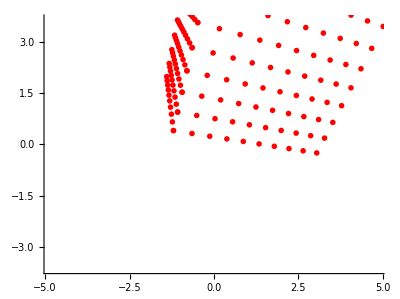

```mathematica
ListPlot[Pts2D,PlotRange->2*MetricPlotRange,PlotStyle->{AbsolutePointSize[4],RGBColor[1,0,0]},AspectRatio->Automatic]
```

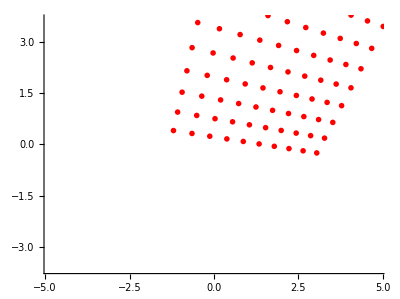

```mathematica
ListPlot[Pts2DSingle,PlotRange->2*MetricPlotRange,PlotStyle->{AbsolutePointSize[4],RGBColor[1,0,0]},AspectRatio->Automatic]
```

#### 4.3.3 We distort the points

```mathematica
CrookedPts2D=If[(Subscript[κ, 1]/.projRules)≠0,N[Map[Distort,Pts2D]//.
Subscript[κ, 1]->Subscript[myκ, 1]],Pts2D];
CrookedPts2DSingle=If[(Subscript[κ, 1]/.projRules)≠0,N[Map[Distort,Pts2DSingle]//.
Subscript[κ, 1]->Subscript[myκ, 1]],Pts2DSingle];
```

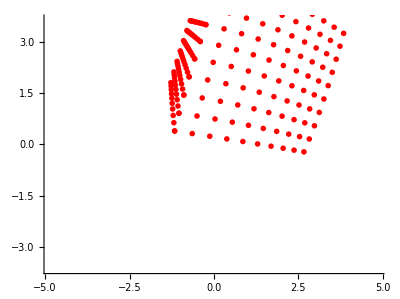

```mathematica
ListPlot[CrookedPts2D,PlotRange->2*MetricPlotRange,PlotStyle->{AbsolutePointSize[4],RGBColor[1,0,0]},AspectRatio->Automatic]
```

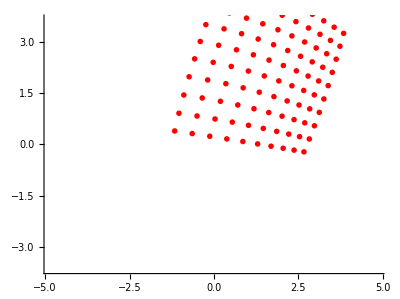

```mathematica
ListPlot[CrookedPts2DSingle,PlotRange->2*MetricPlotRange,PlotStyle->{AbsolutePointSize[4],RGBColor[1,0,0]},AspectRatio->Automatic]
```

#### 4.3.4 We get the positions in (integer) pixels in the image and clip out points

Apply the "integer" mm-to-pixel mapping to our lists of image points

```mathematica
ImageGrid=N[Map[mm2pixel,Pts2D]//.projRules];
ImageGridSingle=N[Map[mm2pixel,Pts2DSingle]//.projRules];
CrookedImageGrid=N[Map[mm2pixel,CrookedPts2D]//.projRules];
CrookedImageGridSingle=N[Map[mm2pixel,CrookedPts2DSingle]//.projRules];
```

I build "boolean" tables indicating for each point whether it falls within image boundaries

```mathematica
PointIsIn=N[Map[isItIn,ImageGrid]//.projRules];
PointIsInSingle=N[Map[isItIn,ImageGridSingle]//.projRules];
CrookedPointIsIn=N[Map[isItIn,CrookedImageGrid]//.projRules];CrookedPointIsInSingle=N[Map[isItIn,CrookedImageGridSingle]//.projRules];
```

We apply this function to our set of points to eliminate the ones that are not visible.

```mathematica
GridPtsIn=ImageGrid;
PtsWorldIn=PtsWorld;
For[i=Dimensions[ImageGrid][[1]],i>0,i--,
If[PointIsIn[[i]]==0,
GridPtsIn=Drop[GridPtsIn,{i,i}];
PtsWorldIn=Drop[PtsWorldIn,{i,i}]];]

GridPtsInSingle=ImageGridSingle;
PtsWorldInSingle=PtsWorldSingle;
For[i=Dimensions[ImageGridSingle][[1]],i>0,i--,
If[PointIsInSingle[[i]]==0,
GridPtsInSingle=Drop[GridPtsInSingle,{i,i}];
PtsWorldInSingle=Drop[PtsWorldInSingle,{i,i}]];]

CrookedGridPtsIn=CrookedImageGrid;
CrookedPtsWorldIn=PtsWorld;
For[i=Dimensions[CrookedImageGrid][[1]],i>0,i--,
If[CrookedPointIsIn[[i]]==0,
CrookedGridPtsIn=Drop[CrookedGridPtsIn,{i,i}];
CrookedPtsWorldIn=Drop[CrookedPtsWorldIn,{i,i}]];]

CrookedGridPtsInSingle=CrookedImageGridSingle;
CrookedPtsWorldInSingle=PtsWorldSingle;
For[i=Dimensions[CrookedImageGridSingle][[1]],i>0,i--,
If[CrookedPointIsInSingle[[i]]==0,
CrookedGridPtsInSingle=Drop[CrookedGridPtsInSingle,{i,i}];
CrookedPtsWorldInSingle=Drop[CrookedPtsWorldInSingle,{i,i}]];]
```

Finally, we get an "image" plot
Reminder: Mathematica displays 2D graphics with the y axis pointing up, so the grid below is the symmetric of the one that will appear in the image

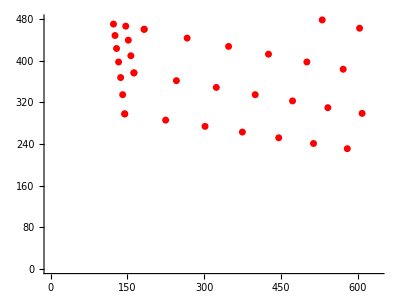

```mathematica
ListPlot[GridPtsIn,PlotRange->PixelPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

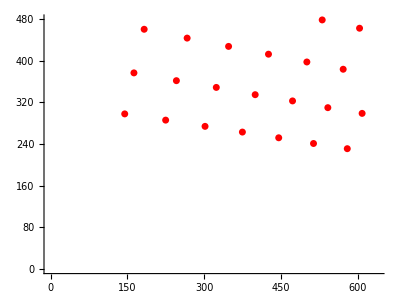

```mathematica
ListPlot[GridPtsInSingle,PlotRange->PixelPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

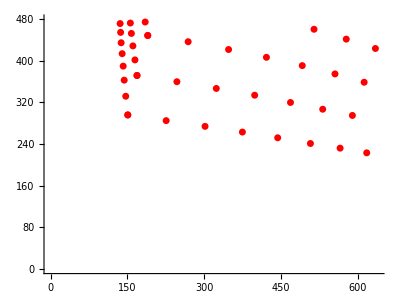

```mathematica
ListPlot[CrookedGridPtsIn,PlotRange->PixelPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

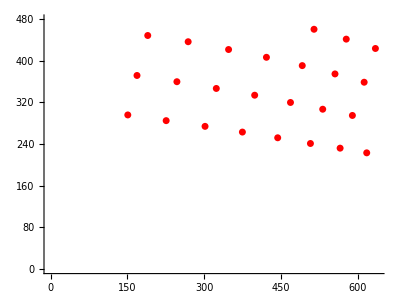

```mathematica
ListPlot[CrookedGridPtsInSingle,PlotRange->PixelPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

#### 4.3.5 We do the same (clip-out) for exact "float" pixels

```mathematica
FlImageGrid=N[Map[mm2flPixel,Pts2D]//.projRules];
FlImageGridSingle=N[Map[mm2flPixel,Pts2DSingle]//.projRules];
```

A function to check whether a  point is out of image boundaries

```mathematica
FlPointIsIn=N[Map[isItIn,FlImageGrid]//.projRules];
FlPointIsInSingle=N[Map[isItIn,FlImageGridSingle]//.projRules];
```

We apply this function to our set of points to eliminate the ones that are not visible.

```mathematica
FlGridPtsIn=FlImageGrid;
FlPtsWorldIn=PtsWorld;
For[i=Dimensions[ImageGrid][[1]],i>0,i--,
If[FlPointIsIn[[i]]==0,
FlGridPtsIn=Drop[FlGridPtsIn,{i,i}];
FlPtsWorldIn=Drop[FlPtsWorldIn,{i,i}]];]
nbFlPtsIn=Dimensions[FlGridPtsIn][[1]];

FlGridPtsInSingle=FlImageGridSingle;
FlPtsWorldInSingle=PtsWorldSingle;
For[i=Dimensions[ImageGridSingle][[1]],i>0,i--,
If[FlPointIsInSingle[[i]]==0,
FlGridPtsInSingle=Drop[FlGridPtsInSingle,{i,i}];
FlPtsWorldInSingle=Drop[FlPtsWorldInSingle,{i,i}]];]
nbFlPtsInSingle=Dimensions[FlGridPtsInSingle][[1]];
```

Finally, we get an "image" plot
Reminder: Mathematica displays 2D graphics with the y axis pointing up, so the grid below is the symmetric of the one that will appear in the image

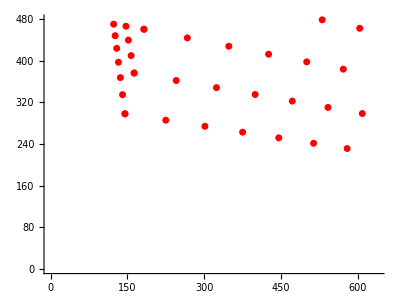

```mathematica
ListPlot[FlGridPtsIn,PlotRange->PixelPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

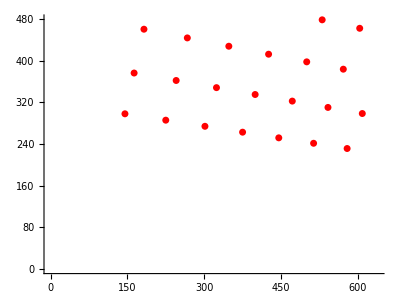

```mathematica
ListPlot[FlGridPtsInSingle,PlotRange->PixelPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

#### 4.3.6 For more verification, we convert back to metric

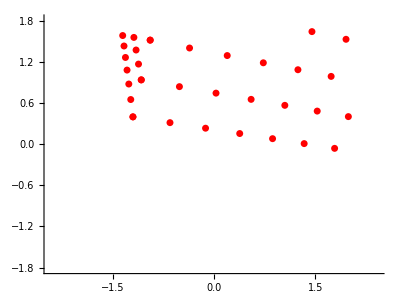

```mathematica
FlMetricPtsIn=N[Map[flPixel2mm,FlGridPtsIn]//.projRules];
ListPlot[FlMetricPtsIn,PlotRange->MetricPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

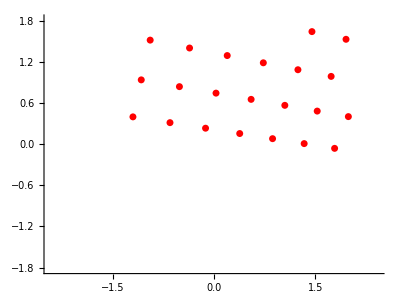

```mathematica
FlMetricPtsInSingle=N[Map[flPixel2mm,FlGridPtsInSingle]//.projRules];
ListPlot[FlMetricPtsInSingle,PlotRange->MetricPlotRange,PlotStyle->{AbsolutePointSize[5],RGBColor[1,0,0]},AspectRatio->Automatic]
```

## 5. Calibration Calculations

### 5.1 Build and check the matrix of the homogeneous equation (using "metric" points)

#### 5.1.1 Single calibration plane, using all exact points

```mathematica
AmatSingle=Flatten[Table[{{f*PtsWorld[[i]][[1]],f*PtsWorld[[i]][[2]],f*PtsWorld[[i]][[3]],f,0.,0.,0.,0.,Pts2D[[i]][[1]]*PtsWorld[[i]][[1]],Pts2D[[i]][[1]]*PtsWorld[[i]][[2]],Pts2D[[i]][[1]]*PtsWorld[[i]][[3]],Pts2D[[i]][[1]]},{0.,0.,0.,0.,f*PtsWorld[[i]][[1]],f*PtsWorld[[i]][[2]],f*PtsWorld[[i]][[3]],f,Pts2D[[i]][[2]]*PtsWorld[[i]][[1]],Pts2D[[i]][[2]]*PtsWorld[[i]][[2]],Pts2D[[i]][[2]]*PtsWorld[[i]][[3]],Pts2D[[i]][[2]]}},{i,1,ptsPerGrid}],1]//.projRules;
```

```mathematica
Chop[AmatSingle.fullStateVec/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### 5.1.2 Two calibration planes, using all exact points

```mathematica
Amat=Flatten[Table[{{f*PtsWorld[[i]][[1]],f*PtsWorld[[i]][[2]],f*PtsWorld[[i]][[3]],f,0.,0.,0.,0.,Pts2D[[i]][[1]]*PtsWorld[[i]][[1]],Pts2D[[i]][[1]]*PtsWorld[[i]][[2]],Pts2D[[i]][[1]]*PtsWorld[[i]][[3]],Pts2D[[i]][[1]]},{0.,0.,0.,0.,f*PtsWorld[[i]][[1]],f*PtsWorld[[i]][[2]],f*PtsWorld[[i]][[3]],f,Pts2D[[i]][[2]]*PtsWorld[[i]][[1]],Pts2D[[i]][[2]]*PtsWorld[[i]][[2]],Pts2D[[i]][[2]]*PtsWorld[[i]][[3]],Pts2D[[i]][[2]]}},{i,1,totalNbPts}],1]//.projRules;
```

```mathematica
Chop[Amat.fullStateVec/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### 5.1.3 Single calibration plane, using only points that fall inside the image

```mathematica
AmatInSingle=Flatten[Table[{{f*FlPtsWorldInSingle[[i]][[1]],f*FlPtsWorldInSingle[[i]][[2]],f*FlPtsWorldInSingle[[i]][[3]],f,0.,0.,0.,0.,FlMetricPtsInSingle[[i]][[1]]*FlPtsWorldInSingle[[i]][[1]],FlMetricPtsInSingle[[i]][[1]]*FlPtsWorldInSingle[[i]][[2]],FlMetricPtsInSingle[[i]][[1]]*FlPtsWorldInSingle[[i]][[3]],FlMetricPtsInSingle[[i]][[1]]},{0.,0.,0.,0.,f*FlPtsWorldInSingle[[i]][[1]],f*FlPtsWorldInSingle[[i]][[2]],f*FlPtsWorldInSingle[[i]][[3]],f,FlMetricPtsInSingle[[i]][[2]]*FlPtsWorldInSingle[[i]][[1]],FlMetricPtsInSingle[[i]][[2]]*FlPtsWorldInSingle[[i]][[2]],FlMetricPtsInSingle[[i]][[2]]*FlPtsWorldInSingle[[i]][[3]],FlMetricPtsInSingle[[i]][[2]]}},{i,1,nbFlPtsInSingle}],1]//.projRules;
```

```mathematica
Chop[AmatInSingle.fullStateVec/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### 5.1.4 Two calibration planes, using only points that fall inside the image

```mathematica
AmatIn=Flatten[Table[{{f*FlPtsWorldIn[[i]][[1]],f*FlPtsWorldIn[[i]][[2]],f*FlPtsWorldIn[[i]][[3]],f,0.,0.,0.,0.,FlMetricPtsIn[[i]][[1]]*FlPtsWorldIn[[i]][[1]],FlMetricPtsIn[[i]][[1]]*FlPtsWorldIn[[i]][[2]],FlMetricPtsIn[[i]][[1]]*FlPtsWorldIn[[i]][[3]],FlMetricPtsIn[[i]][[1]]},{0.,0.,0.,0.,f*FlPtsWorldIn[[i]][[1]],f*FlPtsWorldIn[[i]][[2]],f*FlPtsWorldIn[[i]][[3]],f,FlMetricPtsIn[[i]][[2]]*FlPtsWorldIn[[i]][[1]],FlMetricPtsIn[[i]][[2]]*FlPtsWorldIn[[i]][[2]],FlMetricPtsIn[[i]][[2]]*FlPtsWorldIn[[i]][[3]],FlMetricPtsIn[[i]][[2]]}},{i,1,nbFlPtsIn}],1]//.projRules;
```

```mathematica
Chop[AmatIn.fullStateVec/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### 5.2 Build and check the matrix and right side term of the scaled LLS system

#### 5.2.1 Single calibration plane, using all exact points

```mathematica
LLSmatSingle=Flatten[Table[{{PtsWorld[[i]][[1]],PtsWorld[[i]][[2]],PtsWorld[[i]][[3]],1.,0.,0.,0.,0.,Pts2D[[i]][[1]]*PtsWorld[[i]][[1]],Pts2D[[i]][[1]]*PtsWorld[[i]][[2]],Pts2D[[i]][[1]]*PtsWorld[[i]][[3]]},{0.,0.,0.,0.,PtsWorld[[i]][[1]],PtsWorld[[i]][[2]],PtsWorld[[i]][[3]],1.,Pts2D[[i]][[2]]*PtsWorld[[i]][[1]],Pts2D[[i]][[2]]*PtsWorld[[i]][[2]],Pts2D[[i]][[2]]*PtsWorld[[i]][[3]]}},{i,1,ptsPerGrid}],1]//.projRules;BmatSingle=Flatten[Table[{Pts2D[[i]][[1]],Pts2D[[i]][[2]]},{i,1,ptsPerGrid}],1]//.projRules;
```

```mathematica
Chop[LLSmatSingle.partialScaledStateVec-BmatSingle/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sol=LinearSolve[LLSmatSingle,BmatSingle]
```

{0.00267423,0.00106922,-0.00267423,-1.2,-0.000389268,0.00338268,0.000389268,0.4,-0.000104355,0.00023097,0.000104355}

```mathematica
partialScaledStateVec
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052}

```mathematica
Chop[partialScaleToFullStateVect[sol]-fullStateVec]
```

{-0.074842,0.0226714,-0.188249,-25.4443,0.356369,0.071725,0.372877,8.48144,-0.609095,0.0391791,-0.573692,-169.629}

#### 5.1.2 Two calibration planes, using all exact points

```mathematica
LLSmat=Flatten[Table[{{PtsWorld[[i]][[1]],PtsWorld[[i]][[2]],PtsWorld[[i]][[3]],1.,0.,0.,0.,0.,Pts2D[[i]][[1]]*PtsWorld[[i]][[1]],Pts2D[[i]][[1]]*PtsWorld[[i]][[2]],Pts2D[[i]][[1]]*PtsWorld[[i]][[3]]},{0.,0.,0.,0.,PtsWorld[[i]][[1]],PtsWorld[[i]][[2]],PtsWorld[[i]][[3]],1.,Pts2D[[i]][[2]]*PtsWorld[[i]][[1]],Pts2D[[i]][[2]]*PtsWorld[[i]][[2]],Pts2D[[i]][[2]]*PtsWorld[[i]][[3]]}},{i,1,totalNbPts}],1]//.projRules;Bmat=Flatten[Table[{Pts2D[[i]][[1]],Pts2D[[i]][[2]]},{i,1,totalNbPts}],1]//.projRules;
```

```mathematica
Chop[LLSmat.partialScaledStateVec-Bmat/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sol=LinearSolve[LLSmat,Bmat]
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052}

```mathematica
partialScaledStateVec
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052}

```mathematica
Chop[partialScaleToFullStateVect[sol]-fullStateVec]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

#### 5.1.3 Single calibration plane, using only exact points that fall inside the image

```mathematica
LLSmatInSingle=Flatten[Table[{{FlPtsWorldInSingle[[i]][[1]],FlPtsWorldInSingle[[i]][[2]],FlPtsWorldInSingle[[i]][[3]],1.,0.,0.,0.,0.,FlMetricPtsInSingle[[i]][[1]]*FlPtsWorldInSingle[[i]][[1]],FlMetricPtsInSingle[[i]][[1]]*FlPtsWorldInSingle[[i]][[2]],FlMetricPtsInSingle[[i]][[1]]*FlPtsWorldInSingle[[i]][[3]]},{0.,0.,0.,0.,FlPtsWorldInSingle[[i]][[1]],FlPtsWorldInSingle[[i]][[2]],FlPtsWorldInSingle[[i]][[3]],1.,FlMetricPtsInSingle[[i]][[2]]*FlPtsWorldInSingle[[i]][[1]],FlMetricPtsInSingle[[i]][[2]]*FlPtsWorldInSingle[[i]][[2]],FlMetricPtsInSingle[[i]][[2]]*FlPtsWorldInSingle[[i]][[3]]}},{i,1,nbFlPtsInSingle}],1]//.projRules;
BmatInSingle=Flatten[Table[{FlMetricPtsInSingle[[i]][[1]],FlMetricPtsInSingle[[i]][[2]]},{i,1,nbFlPtsInSingle}],1]//.projRules;
```

```mathematica
Chop[LLSmatInSingle.partialScaledStateVec-BmatInSingle/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sol=LinearSolve[LLSmatInSingle,BmatInSingle]
```

{0.00267423,0.00106922,-0.00267423,-1.2,-0.000389268,0.00338268,0.000389268,0.4,-0.000104355,0.00023097,0.000104355}

```mathematica
partialScaledStateVec
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052}

```mathematica
Chop[partialScaleToFullStateVect[sol]-fullStateVec]
```

{-0.074842,0.0226714,-0.188249,-25.4443,0.356369,0.071725,0.372877,8.48144,-0.609095,0.0391791,-0.573692,-169.629}

#### 5.1.4 Two calibration planes, using only exact points that fall inside the image

```mathematica
LLSmatIn=Flatten[Table[{{FlPtsWorldIn[[i]][[1]],FlPtsWorldIn[[i]][[2]],FlPtsWorldIn[[i]][[3]],1.,0.,0.,0.,0.,FlMetricPtsIn[[i]][[1]]*FlPtsWorldIn[[i]][[1]],FlMetricPtsIn[[i]][[1]]*FlPtsWorldIn[[i]][[2]],FlMetricPtsIn[[i]][[1]]*FlPtsWorldIn[[i]][[3]]},{0.,0.,0.,0.,FlPtsWorldIn[[i]][[1]],FlPtsWorldIn[[i]][[2]],FlPtsWorldIn[[i]][[3]],1.,FlMetricPtsIn[[i]][[2]]*FlPtsWorldIn[[i]][[1]],FlMetricPtsIn[[i]][[2]]*FlPtsWorldIn[[i]][[2]],FlMetricPtsIn[[i]][[2]]*FlPtsWorldIn[[i]][[3]]}},{i,1,nbFlPtsIn}],1]//.projRules;
BmatIn=Flatten[Table[{FlMetricPtsIn[[i]][[1]],FlMetricPtsIn[[i]][[2]]},{i,1,nbFlPtsIn}],1]//.projRules;
```

```mathematica
Chop[LLSmatIn.partialScaledStateVec-BmatIn/.projRules]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sol=LinearSolve[LLSmatIn,BmatIn]
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052}

```mathematica
partialScaledStateVec
```

{0.00320041,0.00106922,-0.00214805,-1.2,-0.00184776,0.00338268,-0.00106922,0.4,0.000191342,0.00023097,0.000400052}

```mathematica
Chop[partialScaleToFullStateVect[sol]-fullStateVec]
```

{0,0,0,0,0,0,0,0,0,0,0,-1.21872×10^-10}

Since we have a solution, I verify that this is the one that a QR factorization would give us

```mathematica
{myQt,myR}=Chop[QRDecomposition[LLSmatIn]];
Dmat=myQt.BmatIn;
qrSol=LinearSolve[myR,Dmat];
Chop[qrSol-partialScaledStateVec]
```

{0,0,0,0,0,0,0,0,0,0,0}

### 5.3 Build and check the "projection matrix" of the DLT algorithm

We simply express that m_i × (P M_i) = 0, where m_i = (x_i,y_i,1), P is the projection matrix, and M_i= (X_i,Y_i,Z_i 1).
Each point gives us three linear equations in terms of the flattened projection matrix, but these equations are linearly dependent, we only use the first two equations.

#### 5.3.1 Single calibration plane, using all float points

```mathematica
FlDLTmatSingle=Flatten[Table[{Flatten[{0,0,0,0,-PtsWorld[[i]],-1,FlImageGrid[[i]][[2]]*PtsWorld[[i]],FlImageGrid[[i]][[2]]}],Flatten[{PtsWorld[[i]],1,0,0,0,0,-FlImageGrid[[i]][[1]]*PtsWorld[[i]],-FlImageGrid[[i]][[1]]}]},{i,1,ptsPerGrid}],1]//.projRules;
```

```mathematica
Chop[FlDLTmatSingle.ProjVect,10^-8]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Now use SVD and get the eigenvector associated to the smallest singular value

```mathematica
S1[[9]][[9]]
```

1888.78

```mathematica
{U1,S1,V1}=SingularValueDecomposition[FlDLTmatSingle];
```

```mathematica
{K,R}=DecomposeProjVect[Transpose[V1][[12]]];
MatrixForm[K]
MatrixForm[R]
MatrixForm[RotMat/.projRules]
```

(0.00164668 | -0.00015641 | 0.00154661
-8.49122×10^-20 | -0.00354808 | 0.00472695
4.11375×10^-23 | 1.48341×10^-23 | 1.96136×10^-6)

(0.695291 | 0.402611 | -0.595378
0.53409 | -0.843755 | 0.0531476
-0.480955 | -0.354939 | -0.801686)

(0.800103 | 0.267306 | -0.537013
-0.46194 | 0.845671 | -0.267306
0.382683 | 0.46194 | 0.800103)

```mathematica
rankMat={V1[[10]],V1[[11]],V1[[12]],ProjVect};
{U2,S2,V2}=SingularValueDecomposition[rankMat];
MatrixForm[Take[Transpose[S2],{1,4}]]
```

(663539. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 0.999676)

The eigenvector compared to the solution, normalized

```mathematica
Chop[Transpose[V1][[12]]-ProjVect/Norm[ProjVect]]
```

{0.0015361,0.000491982,-0.00355622,0.876833,-0.00511696,0.00263189,-0.00473627,1.79751,-1.52006×10^-6,-1.39234×10^-6,-2.77821×10^-6,0.00602823}

#### 5.3.2 Two calibration planes, using all float points

```mathematica
FlDLTmat=Flatten[Table[{Flatten[{0,0,0,0,-PtsWorld[[i]],-1,FlImageGrid[[i]][[2]]*PtsWorld[[i]],FlImageGrid[[i]][[2]]}],Flatten[{PtsWorld[[i]],1,0,0,0,0,-FlImageGrid[[i]][[1]]*PtsWorld[[i]],-FlImageGrid[[i]][[1]]}]},{i,1,totalNbPts}],1]//.projRules;
```

```mathematica
Chop[FlDLTmat.ProjVect,10^-8]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Now use SVD and get the eigenvector associated to the smallest singular value

```mathematica
{U1,S1,V1}=SingularValueDecomposition[FlDLTmat];
```

```mathematica
S1[[11]][[11]]
```

5.62773

```mathematica
{K,R}=DecomposeProjVect[Transpose[V1][[12]]];
MatrixForm[K]
MatrixForm[R]
MatrixForm[RotMat/.projRules]
```

(0.00175368 | 2.36998×10^-16 | 0.000482262
-6.09225×10^-20 | -0.00175368 | 0.000361697
-4.91042×10^-23 | -2.31085×10^-23 | 1.50707×10^-6)

(0.800103 | 0.267306 | -0.537013
0.46194 | -0.845671 | 0.267306
-0.382683 | -0.46194 | -0.800103)

(0.800103 | 0.267306 | -0.537013
-0.46194 | 0.845671 | -0.267306
0.382683 | 0.46194 | 0.800103)

The eigenvector compared to the solution, normalized

```mathematica
Chop[Transpose[V1][[12]]-ProjVect/Norm[ProjVect]]
```

{0.00243714,0.000491986,-0.00265522,0.87684,-0.00189702,0.00263191,-0.00151633,1.79752,-1.15346×10^-6,-1.39235×10^-6,-2.41162×10^-6,0.00602828}

```mathematica
{K,R}=DecomposeProjVect[Transpose[V1][[12]]];
MatrixForm[K]
MatrixForm[R]
```

(0.00175368 | 2.36998×10^-16 | 0.000482262
-6.09225×10^-20 | -0.00175368 | 0.000361697
-4.91042×10^-23 | -2.31085×10^-23 | 1.50707×10^-6)

(0.800103 | 0.267306 | -0.537013
0.46194 | -0.845671 | 0.267306
-0.382683 | -0.46194 | -0.800103)

```mathematica
MatrixForm[Chop[R-RotMat/.projRules]]
```

(0 | 0 | 0
0.92388 | -1.69134 | 0.534612
-0.765367 | -0.92388 | -1.60021)

#### 5.3.3 Single calibration plane, using all integer points

```mathematica
DLTmatSingle=Flatten[Table[{Flatten[{0,0,0,0,-PtsWorld[[i]],-1,ImageGrid[[i]][[2]]*PtsWorld[[i]],ImageGrid[[i]][[2]]}],Flatten[{PtsWorld[[i]],1,0,0,0,0,-ImageGrid[[i]][[1]]*PtsWorld[[i]],-ImageGrid[[i]][[1]]}]},{i,1,ptsPerGrid}],1]//.projRules;
```

```mathematica
DLTmatSingle.ProjVect
```

{363.636,-909.091,-204.797,-466.226,228.577,404.903,-461.468,-796.608,-233.189,-237.727,913.413,-377.616,727.887,658.5,-914.994,327.975,527.416,589.066,428.988,-1184.36,-535.497,-687.442,684.315,880.855,-871.999,-692.646,712.912,133.731,-728.755,1011.86,970.805,-573.366,-606.666,-760.518,957.089,199.948,-1006.64,-207.063,170.86,-50.8438,206.252,762.569,686.694,-682.285,641.461,-949.194,-54.6723,-413.835,501.453,548.113,239.71,-509.155,-965.128,137.197,1068.94,83.1062,-118.93,-1047.11,-304.99,845.074,43.9925,-559.059,-784.293,345.961,-26.3831,-780.486,400.368,-729.826,370.736,122.265,-240.507,-600.728,483.994,685.449,459.917,-438.298,-437.964,-220.747,-167.07,-1080.15,432.836,516.182,-508.956,-187.18,385.898,-602.268,-578.725,618.076,126.331,-681.432,569.519,667.716,625.615,468.491,169.391,235.02,-924.377,-408.374,-682.402,261.144,-479.198,57.5847,-630.634,-794.296,-348.516,-830.286,241.928,-551.29,-805.038,-458.212,-15.3581,810.302,706.972,-929.423,-709.014,-466.297,-538.804,-38.2547,-811.623,-20.9727,763.001,-558.471,513.658,-265.135,-566.643,-212.548,690.606,682.642,782.962,168.307,-540.028,-588.716,140.596,-254.626,-928.061,794.9,-160.071,265.994,484.634,-382.316,-237.437,-232.766,-83.2129,776.683,-203.946,627.329,790.103,208.002,-590.156,574.506,450.619,-497.736,381.598,-104.024,759.487,-427.193,-389.839,-119.247,464.449,444.136,459.635,411.079,-134.645,220.127,-447.881,-463.432,-730.523,750.843,379.616,136.767,-551.453,251.749,-507.159,594.887,387.27,665.275,227.002,-37.9888,582.933,-194.459,-364.706,-626.936,-190.284,485.696,-471.713,479.02,-83.0622,-21.9365,725.215,-225.181,117.577,-756.842,-654.821,-616.217,-173.857,-304.209,-275.073,-321.722,543.139,582.399}

Now use SVD and get the eigenvector associated to the smallest singular value

```mathematica
{U1,S1,V1}=SingularValueDecomposition[DLTmatSingle];
```

```mathematica
{K,R}=DecomposeProjVect[Transpose[V1][[12]]];
MatrixForm[K]
MatrixForm[R]
```

(-7.21315×10^-15 | -1.55852×10^-14 | -0.129278
3.3063×10^-31 | -3.6009×10^-14 | 0.991608
-1.31118×10^-20 | -3.83623×10^-21 | 0.00027978)

(0.678656 | -0.280807 | -0.678656
0.198561 | 0.959764 | -0.198561
0.707107 | 3.0333×10^-14 | 0.707107)

The eigenvector, normalized

```mathematica
Transpose[V1][[12]]
```

{-0.0914134,-1.6854×10^-14,-0.0914134,3.13798×10^-12,0.701173,-4.48164×10^-15,0.701173,1.08642×10^-12,0.000197834,8.48656×10^-18,0.000197834,-6.43186×10^-15}

The eigenvector compared to the solution, normalized

```mathematica
Chop[Transpose[V1][[12]]-ProjVect/Norm[ProjVect]]
```

{-0.0901948,0.000245993,-0.092741,0.43842,0.700224,0.00131595,0.700415,0.898761,0.000197257,-6.96175×10^-7,0.000196628,0.00301414}

#### 5.3.2 Two calibration planes, using all integer points

```mathematica
DLTmat=Flatten[Table[{Flatten[{0,0,0,0,-PtsWorld[[i]],-1,ImageGrid[[i]][[2]]*PtsWorld[[i]],ImageGrid[[i]][[2]]}],Flatten[{PtsWorld[[i]],1,0,0,0,0,-ImageGrid[[i]][[1]]*PtsWorld[[i]],-ImageGrid[[i]][[1]]}]},{i,1,totalNbPts}],1]//.projRules;
```

```mathematica
{U1,S1,V1}=SingularValueDecomposition[DLTmat];
```

```mathematica
{K,R}=DecomposeProjVect[Transpose[V1][[12]]];
MatrixForm[K]
MatrixForm[R]
```

(0.00175427 | -1.36108×10^-7 | 0.00048238
-7.71649×10^-20 | -0.00175434 | 0.000362187
-1.00774×10^-23 | 5.21823×10^-23 | 1.50763×10^-6)

(0.800143 | 0.267333 | -0.536939
0.461902 | -0.845706 | 0.26726
-0.382645 | -0.46186 | -0.800168)

The eigenvector compared to the solution, normalized

```mathematica
Chop[Transpose[V1][[12]]-ProjVect/Norm[ProjVect]]
```

{0.00243759,0.000492291,-0.00265557,0.876639,-0.00189743,0.00263233,-0.00151684,1.79762,-1.15362×10^-6,-1.39249×10^-6,-2.41216×10^-6,0.00602892}

#### 5.3.3 Single calibration plane, using only points that fall inside the image

#### 5.3.4 Two calibration planes, using only points that fall inside the image

#### 5.3.5 Single calibration plane, using only crooked points that fall inside the image

#### 5.3.4 Two calibration planes, using only crooked points that fall inside the image

## 6. Output of Calibration Data Files

### 6.1 Where we work...

```mathematica
SetDirectory["/SDKs/urivisionLib/SDK/Demos/C++/Computer_Vision/Calibration_3D/Data"];
FileNames[]
```

{calibration.nb,data01.txt,data02.txt,data03.txt,.DS_Store,.svn}

### 6.2 Data file index

```mathematica
dataNum="01";
```

### 5.3 We generate the parameter file

```mathematica
dataFileName = StringJoin["data",StringJoin[dataNum,".txt"]];

strm=OpenWrite[dataFileName,FormatType->OutputForm];
Write[strm,myNcx," ",myNcy," ",mydx," ",mydy," ",myNfx," ",myNfy," ",mydpx," ",mydpy];
Write[strm,nbFlPtsIn];
For[i=1,i≤ptsPerRow^2,i++,
If[flPointIsIn[[i]]==1,
Write[strm,flPtsWorldIn[[i]][[1]]," ",flPtsWorldIn[[i]][[2]]," ",flPtsWorldIn[[i]][[3]]," ",flGridPtsIn[[i]][[1]]," ",flGridPtsIn[[i]][[2]]];];];

Close[strm];
```

Part::partw: Part 61 of {{0, 600., 0}, {0, 750., 0}, {100., 750., -100.}, {200., 750., -200.}, {300., 750., -300.}, {« 1 »}, {500., 750., -500.}, {0, 900., 0}, {100., 900., -100.}, {200., 900., -200.}, « 46 »} does not exist.

General::stop: Further output of Part :: "partw" will be suppressed during this calculation.

```mathematica
dataFileName = StringJoin["dataAndSol",StringJoin[dataNum,".txt"]];

strm=OpenWrite[dataFileName,FormatType->OutputForm];
Write[strm,myψ," ",myθ," ",myφ ," ",Subscript[myT, x]," ",Subscript[myT, y]," ",Subscript[myT, z]];
Write[strm,myNcx," ",myNcy," ",mydx," ",mydy," ",myNfx," ",myNfy," ",mydpx," ",mydpy," ",myCx," ",myCy," ",mysx," ",myFoc," ",Subscript[myκ, 1]];
Write[strm,nbFlPtsIn];
For[i=1,i≤ptsPerRow^2,i++,
If[flPointIsIn[[i]]==1,
Write[strm,flPtsWorldIn[[i]][[1]]," ",flPtsWorldIn[[i]][[2]]," ",flPtsWorldIn[[i]][[3]]," ",flGridPtsIn[[i]][[1]]," ",flGridPtsIn[[i]][[2]]];];];

Close[strm];
```